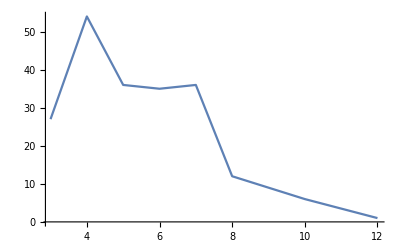

```mathematica
Clear["`*"]
foo[i_,l_]:=Tally@Nest[Flatten@Outer[Plus,#,l]&,l,i-1]
ListLinePlot@Reverse@SortBy[foo[3,{1,1,1,2,2,4}],First]
```

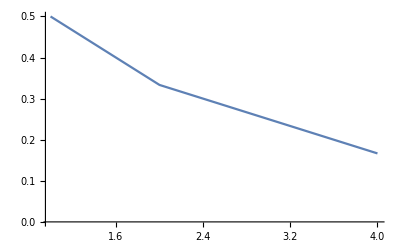
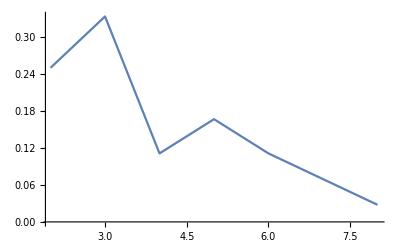
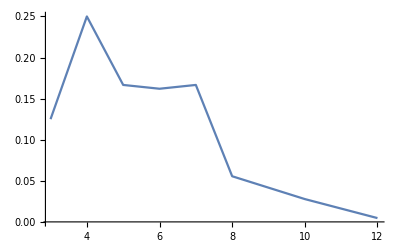
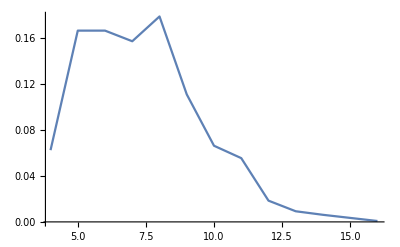
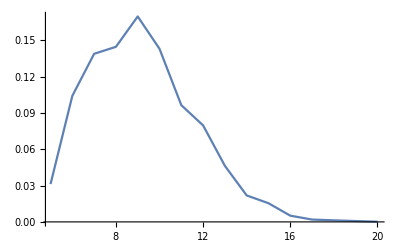
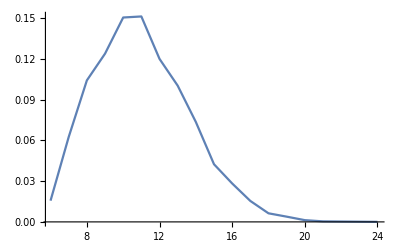
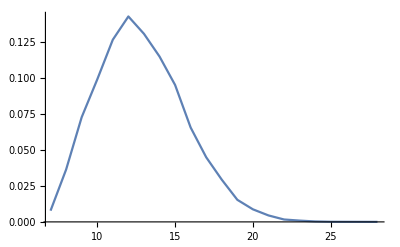
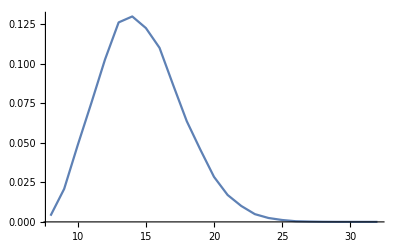

```mathematica
Clear["`*"]
RandomInteger[10,10];
bar[i_,l_]:=Module[{eq,ans},
eq=Inner@@Flatten[{Function[{a,b},b x^a],Transpose@Tally@l,Plus},1];
ans=N@Partition[Flatten@Apply[List,CoefficientRules[eq^i],{1}],2];
ans[[All,2]]=ans[[All,2]]/Total[ans[[All,2]]];
ListLinePlot[ans]]
bar[#,{1,1,1,2,2,4}]&/@Range@12
bar[#,{2,3,5,7,11,13}]&/@Range@12
```

```mathematica
Clear["`*"]
l={1,1,1,2,2,4}
f[x_]:=Inner@@Join[{Function[{a,b},b UnitBox[x-a]]},Transpose@Tally@l,{Plus}]
PiecewiseExpand[DiscreteConvolve[f[m], f[n],m,n],Assumptions->n∈Integers]
PiecewiseExpand[Convolve[f[y],f[x],y,x],Assumptions->x∈Integers]
```

{1,1,1,2,2,4}

Piecewise[{{6, 7/2≤n≤9/2}, {12, 3/2<n≤5/2}, {18, 1/2≤n<3/2}, {0, True}}]

Piecewise[{{6, 7/2≤x≤9/2}, {12, 3/2<x≤5/2}, {18, 1/2≤x<3/2}, {0, True}}]

```mathematica
l={1,1,1,2,2,4}
baz[i_,l_]:=Module[{fun,ZF,exp},
fun[x_]:=Inner@@Join[{Function[{a,b},b UnitBox[x-a]]},Transpose@Tally@l,{Plus}];
ZF[f_,s_,t_,n_]:=InverseZTransform[ZTransform[f,s,t]^(n+1),t,s];
exp=FunctionExpand[ZF[fun[n],n,m,i]/Length[l]^i]]
baz[5.0,{1,1,1,2,2,4}]
```

{1,1,1,2,2,4}

0.000128601 DiscreteDelta[-24.+n]+0.00154321 DiscreteDelta[-22.+n]+0.00231481 DiscreteDelta[-21.+n]+0.00771605 DiscreteDelta[-20.+n]+0.0231481 DiscreteDelta[-19.+n]+0.0379372 DiscreteDelta[-18.+n]+0.0925926 DiscreteDelta[-17.+n]+0.169753 DiscreteDelta[-16.+n]+0.25463 DiscreteDelta[-15.+n]+0.441358 DiscreteDelta[-14.+n]+0.601852 DiscreteDelta[-13.+n]+0.720036 DiscreteDelta[-12.+n]+0.907407 DiscreteDelta[-11.+n]+0.902778 DiscreteDelta[-10.+n]+0.743056 DiscreteDelta[-9.+n]+0.625 DiscreteDelta[-8.+n]+0.375 DiscreteDelta[-7.+n]+0.09375 DiscreteDelta[-6.+n]

```mathematica
Clear["`*"]
ZF[f_,s_,t_,n_]:=InverseZTransform[ZTransform[f,s,t]^(n+1),t,s]
LF[f_,s_,t_,n_]:=InverseLaplaceTransform[LaplaceTransform[f,s,t]^(n+1),t,s];
FF[f_,s_,t_,n_]:=InverseFourierTransform[FourierTransform[f,s,t]^(n+1),t,s];
Timing[ZF[{1/8 UnitBox[(x-8)/8],2/3 ⅇ^(-x λ) λ,,(√2)/(π (1+x^4))},x,m,10];]

Timing[LF[{1/8 UnitBox[(x-8)/8],2/3 ⅇ^(-x λ) λ,,(√2)/(π (1+x^4))},x,m,10];]
Timing[FF[{1/8 UnitBox[(x-8)/8],2/3 ⅇ^(-x λ) λ,,(√2)/(π (1+x^4))},x,m,10];]
```

{2.65625,Null}

{4.90625,Null}

{19.7031,Null}

```mathematica
UnitBox[n/7]/7
```

1/7 UnitBox[n/7]

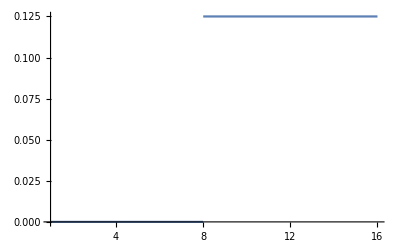

```mathematica
Plot[1/8 UnitBox[(n-12)/8],{n,1,16}]
```

```mathematica
Simplify[LaplaceTransform[PDF[NormalDistribution[μ,σ],s],s,t],σ>0]
Simplify[LaplaceTransform[PDF[UniformDistribution[{a,b}],s],s,t]^(n+1),b>a>0]
```

1/2 ⅇ^(1/2 t (-2 μ+t σ^2)) Erfc[(-μ/σ+t σ)/(√2)]

(-(ⅇ^(-a t)-ⅇ^(-b t))/(a t-b t))^(1+n)

```mathematica
Refine[Solve[Array[Function[k,Moment[UniformSumDistribution[n,{a,b}],k]==Moment[NormalDistribution[μ,σ],k]],2,1,And],{μ,σ},Reals],n>0]
UN[a_,b_,n_]:=PDF[NormalDistribution[(a+b)/2 n,(b-a)/(2 √3)√n],x]
```

{{μ→1/2 (a n+b n),σ→-(√(a^2 n-2 a b n+b^2 n))/(2 √3)},{μ→1/2 (a n+b n),σ→(√(a^2 n-2 a b n+b^2 n))/(2 √3)}}